```mathematica
θ=π/6
τ=.
```

π/6

```mathematica
Graphics[{EdgeForm[Thick],RGBColor[1.,0.7408255130846113,0.37500572213321126],Disk[{0,0},1,{-7π/6,π/6}]}]
```

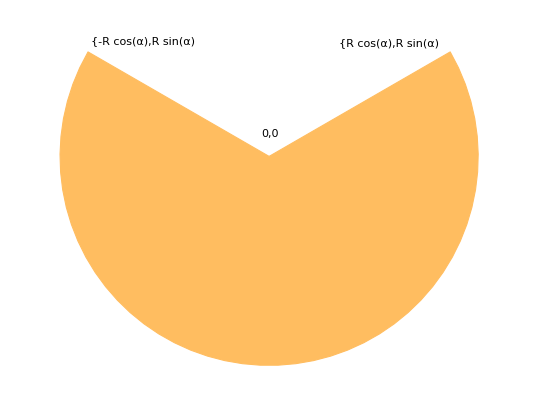
```mathematica
-Graphics-
θ=.
Considero la formula per la pressione trovata seguendo il calcolo di Fily
 p=(1+√(2π)(√(Diff τ))/(2 R))Diff Underscript[ρ, Bulk]
```

Considero la formula per la pressione trovata seguendo il calcolo di Fily

Diff (1+(√(π/2) √(Diff τ))/R) ρ_Bulk

```mathematica
La forza verso il basso diventa, lungo l'arco
F1=2 p * R Cos[θ]
```

```mathematica
2 Diff R (1+(√(π/2) √(Diff τ))/R) Cos[θ] Underscript[ρ, Bulk]
La forza lungo i segmenti diventa
F2=2Diff R Cos[θ] Underscript[ρ, Bulk]
```

```mathematica
Lungo i due corners  positivi in R Cos[θ] , R Sin[θ]
F3=√(2π)Diff L Cos[π/4] Underscript[ρ, Bulk]
La forza nel corner negativo
F=-Simplify[-F1+F2 +2*F3]
```

R^2 Cos[θ] Sin[θ] , Lungo i due corners  positivi in

Diff L √π ρ_Bulk

La forza nel corner negativo

-Diff √π (2 L-√2 √(Diff τ) Cos[θ]) ρ_Bulk